# Lab 5 - Joe, Zack, Christopher

## Fall

### Simulation

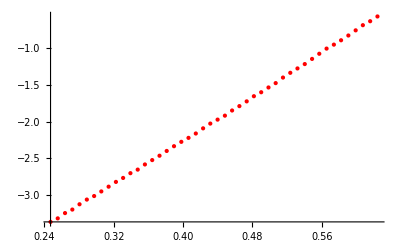

```mathematica
fallexperiment=ListPlot[fall,PlotStyle->Red]
```

```mathematica
vf=-7.814;
g=9.8;
m=.01436;
c2=m*g/vf^2
```

0.0023048

### Data

```mathematica
falldata={{"VideoAnalysis: Time (s)","VideoAnalysis: Y (m)","VideoAnalysis: X (m)","VideoAnalysis: Y Velocity (m/s)","VideoAnalysis: X Velocity (m/s)","VideoAnalysis: X 2 (m)","VideoAnalysis: Y 2 (m)","VideoAnalysis: X Velocity 2 (m/s)","VideoAnalysis: Y Velocity 2 (m/s)"},{0.22201978954,-3.56457544326,0.0668035685945,7.4190754313,-1.12076205403,"","","",""},{0.230312549081,-3.50854961069,0.0587998782265,7.96242133952,-1.19655835468,"","","",""},{0.238730956494,-3.42851270701,0.0427924974906,8.02811557827,-0.954071364114,"","","",""},{0.247149363908,-3.36448318407,0.0427924974906,7.19782170787,-0.690277570351,"","","",""},{0.255442123449,-3.31646104186,0.0347888071226,7.17227660574,-0.744157869596,"","","",""},{0.263860530862,-3.24442782855,0.0267851167546,7.18088107656,-0.47695597814,"","","",""},{0.272278938275,-3.19640568634,0.0267851167546,7.30468541004,-0.238673828167,"","","",""},{0.280571697817,-3.12437247303,0.0267851167546,7.59434478869,-0.393794608895,"","","",""},{0.28899010523,-3.06034295008,0.0187814263866,6.9840416838,-0.448999433735,"","","",""},{0.297408512643,-3.01232080787,0.0187814263866,6.9502033858,-0.478331664999,"","","",""},{0.305701272185,-2.94943467406,0.0122329586205,7.40265646991,-0.61423281112,"","","",""},{0.314119679598,-2.88457359935,0.0068278690621,7.50465490536,-0.533791997229,"","","",""},{0.322538087011,-2.81971252465,0.00142277950369,7.22265569856,-0.272989758041,"","","",""},{0.330830846553,-2.76566162907,0.00142277950369,7.08601376278,0.0721676944251,"","","",""},{0.339249253966,-2.70080055437,0.0068278690621,6.94361309872,-0.0179240652179,"","","",""},{0.347667661379,-2.65215474834,0.00142277950369,7.15757576099,-0.161720889184,"","","",""},{0.35596042092,-2.58188858408,0.00142277950369,7.46316060547,-0.0537050643234,"","","",""},{0.364378828334,-2.52243259894,0.00142277950369,7.28377207,-0.0179240652179,"","","",""},{0.372797235747,-2.4629766138,0.00142277950369,7.44469797537,-0.0179240652179,"","","",""},{0.381089995288,-2.3981155391,0.00142277950369,7.5526466689,-0.0716291295413,"","","",""},{0.389508402701,-2.3332544644,0.00142277950369,7.31854809554,-0.232345045156,"","","",""},{0.397926810115,-2.27379847925,-0.00398231005473,6.99592200314,-0.233350018726,"","","",""},{0.406219569656,-2.21974758367,-0.00398231005473,7.04962706746,-0.0895531947592,"","","",""},{0.414637977069,-2.16029159853,-0.00398231005473,7.53296907547,-0.0897550934973,"","","",""},{0.423056384482,-2.09002543427,-0.00398231005473,7.69644349287,-0.233350018726,"","","",""},{0.431349144024,-2.02516435957,-0.00938739961314,7.21134795664,-0.233350018726,"","","",""},{0.439767551437,-1.97111346398,-0.00938739961314,6.87285417534,-0.0718310282794,"","","",""},{0.44818595885,-1.9170625684,-0.00938739961314,7.30143971629,-0.0179240652179,"","","",""},{0.456478718392,-1.84679640414,-0.00938739961314,7.58849479934,0,"","","",""},{0.464897125805,-1.787340419,-0.00938739961314,7.57002407822,0,"","","",""},{0.473315533218,-1.7224793443,-0.00938739961314,7.78606381896,0,"","","",""},{0.48160829276,-1.65221318004,-0.00938739961314,7.48047897448,0,"","","",""},{0.490026700173,-1.59816228445,-0.00938739961314,7.30156136781,0,"","","",""},{0.498445107586,-1.53330120975,-0.00938739961314,7.53425117013,0,"","","",""},{0.506737867127,-1.47384522461,-0.00938739961314,7.92925494671,-0.0179240652179,"","","",""},{0.515156274541,-1.39817397079,-0.00938739961314,8.03350729622,-0.0718310282794,"","","",""},{0.523574681954,-1.33331289609,-0.00938739961314,7.58795623445,-0.215425953508,"","","",""},{0.531867441495,-1.27385691095,-0.0147924891716,7.40837841138,-0.143796823966,"","","",""},{0.540285848908,-1.2144009258,-0.0147924891716,7.74832739291,0.214420979938,"","","",""},{0.548704256322,-1.14413476154,-0.00938739961314,8.16260496543,0.377146842692,"","","",""},{0.556997015863,-1.07386859729,-0.00398231005473,8.10889990111,0.0716291295413,"","","",""},{0.565415423276,-1.00360243303,-0.00938739961314,7.51598234775,-0.142589951659,"","","",""},{0.573833830689,-0.949551537442,-0.00938739961314,7.15710432744,-0.0537050643234,"","","",""},{0.582126590231,-0.890095552299,-0.00938739961314,7.48054610581,-0.0179240652179,"","","",""},{0.590544997644,-0.825234477598,-0.00938739961314,7.89105211197,0,"","","",""},{0.598963405057,-0.754968313339,-0.00938739961314,8.05519483679,0.0179240652179,"","","",""},{0.607256164599,-0.68470214908,-0.00938739961314,7.60588029967,0.0716291295413,"","","",""},{0.615674572012,-0.630651253495,-0.00938739961314,7.46314748959,0.232345045156,"","","",""},{0.624092979425,-0.565790178794,-0.00398231005473,7.98302714236,0.233350018726,"","","",""},{0.632385738967,-0.495524014535,-0.00398231005473,8.34224991984,0.0716291295413,"","","",""},{0.64080414638,-0.419852760717,-0.00398231005473,8.07042753156,0,"","","",""},{0.649222553793,-0.360396775575,-0.00398231005473,7.80284362308,-0.0537050643234,"","","",""},{0.657515313334,-0.295535700874,-0.00398231005473,8.12689109766,-0.143796823966,"","","",""},{0.665933720748,-0.219864447056,-0.00938739961314,8.05250346634,0.0718310282794,"","","",""},{0.674352128161,-0.160408461913,-0.00398231005473,7.82110485919,0.39507090791,"","","",""},{0.682644887702,-0.090142297654,0.00142277950369,7.23176345229,0.287055083049,"","","",""},{0.691063295115,-0.0144710438362,0.00142277950369,4.06821553801,0.0969677804018,"","","",""},{0.699481702529,-0.0144710438362,0.00142277950369,0.169267864013,0.0269534815307,"","","",""},{0.70777446207,-0.0469015811867,0.00142277950369,-2.31545108248,0,"","","",""}};
```

```mathematica
fall=Table[{falldata[[n,1]],falldata[[n,2]]},{n,5,50}]
```

{{0.247149,-3.36448},{0.255442,-3.31646},{0.263861,-3.24443},{0.272279,-3.19641},{0.280572,-3.12437},{0.28899,-3.06034},{0.297409,-3.01232},{0.305701,-2.94943},{0.31412,-2.88457},{0.322538,-2.81971},{0.330831,-2.76566},{0.339249,-2.7008},{0.347668,-2.65215},{0.35596,-2.58189},{0.364379,-2.52243},{0.372797,-2.46298},{0.38109,-2.39812},{0.389508,-2.33325},{0.397927,-2.2738},{0.40622,-2.21975},{0.414638,-2.16029},{0.423056,-2.09003},{0.431349,-2.02516},{0.439768,-1.97111},{0.448186,-1.91706},{0.456479,-1.8468},{0.464897,-1.78734},{0.473316,-1.72248},{0.481608,-1.65221},{0.490027,-1.59816},{0.498445,-1.5333},{0.506738,-1.47385},{0.515156,-1.39817},{0.523575,-1.33331},{0.531867,-1.27386},{0.540286,-1.2144},{0.548704,-1.14413},{0.556997,-1.07387},{0.565415,-1.0036},{0.573834,-0.949552},{0.582127,-0.890096},{0.590545,-0.825234},{0.598963,-0.754968},{0.607256,-0.684702},{0.615675,-0.630651},{0.624093,-0.56579}}

## Trial 1

### Simulation

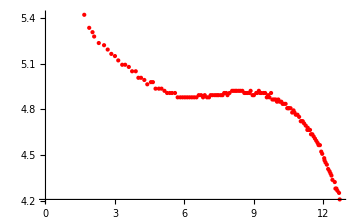

```mathematica
trial1experiment=ListPlot[trial1,PlotStyle->Red]
```

```mathematica
vx==D[32.3-286.4*t+840.8*t^2-766.3*t^3,t]/.t->.3244
```

General::ivar: 1.4044 is not a valid variable.

General::ivar: 0.3244 is not a valid variable.

4.42722==∂_0.3244 (-834.193)

```mathematica
vy==D[42.44-292.1*t+770.1*t^2-682.8*t^3,t]/.t->.3244
```

vy==-8.02323

```mathematica
Clear[t]
```

```mathematica
Manipulate[
g=9.8;
m=.01436;
r=.05;
c2=.0023048;
ρ=1.2041;
period=.4534-.4236;
ω=2*π/period;
vx=17.1855;
vy=-8.0232;
x=1.6754913375;
y=5.4207992383;
ti=.3244;
tf=1.403;
dt=.01;

(* define an array where we store the results of the simulation *) 
modeldatatrial1 ={{x,y}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t≤tf,
θ=ArcTan[vy/vx];
v=Sqrt[vx^2+vy^2];

fd=c2*v^2;
fs=2*π*ρ*v*cl*r^3*ω ;
fg=-m*g;

ax=(fd*Cos[θ+π]+fs*Cos[θ+π/2])/m;
vx=vx+ax*dt;
x=x+vx*dt;

ay=(fd*Sin[θ+π]+fs*Sin[θ+π/2]+fg)/m;
vy=vy+ay*dt;
y=y+vy*dt;

t= t + dt;
(* add the results of the calculation step to the array *)
modeldatatrial1 = Append[modeldatatrial1,{x,y}];
];
(* plot the simulation and compare with the exact result *)
dataplottrial1 = ListPlot[modeldatatrial1];
Show[{dataplottrial1,trial1experiment},PlotRange->All],{cl,0,.2}]
```

### Data

```mathematica
trial1data={{"VideoAnalysis: Time (s)","VideoAnalysis: X (m)","VideoAnalysis: Y (m)","VideoAnalysis: X Velocity (m/s)","VideoAnalysis: Y Velocity (m/s)"},{0.324411954245,1.6754913375,5.4207992383,23.5728092308,-8.64951285141},{0.332431126148,1.88942026211,5.33522766846,20.0546002868,-6.41629535389},{0.34069330326,2.03203954518,5.30670381184,16.5561725298,-4.48415086313},{0.348712475163,2.10334918671,5.27817995523,18.490009339,-4.17358571611},{0.356731647065,2.30301618301,5.23539417031,23.1662964331,-3.51265057349},{0.364993824177,2.53120703592,5.221132242,22.743029357,-3.01989704871},{0.37301299608,2.6880882473,5.19260838539,20.3596685002,-3.16589158824},{0.381275173192,2.84496945867,5.16408452877,19.4158101436,-2.83024501933},{0.389294345094,3.00185067005,5.14982260047,18.8908970723,-2.79599451409},{0.397313516997,3.14446995312,5.12129874385,18.9436367264,-2.87866105312},{0.405575694109,3.3156130928,5.09277488724,18.4567449374,-2.00269381624},{0.413594866012,3.44397044757,5.09277488724,18.1053800888,-1.51694962619},{0.421614037914,3.60085165894,5.07851295893,18.1969935748,-2.14454635526},{0.429876215026,3.74347094201,5.04998910232,17.8252032955,-2.04538349768},{0.437895386929,3.90035215339,5.04998910232,16.5601606111,-2.38628074739},{0.446157564041,4.01444757985,5.0072033174,15.1753822795,-2.29163859806},{0.454176735943,4.1285430063,5.0072033174,15.9007298204,-1.56512782425},{0.462195907846,4.27116228937,4.99294138909,16.4544188515,-1.85267619431},{0.470458084958,4.39951964413,4.96441753248,16.5982179845,-0.976708957675},{0.478477256861,4.55640085551,4.97867946078,15.1633910353,-0.383899277881},{0.486496428763,4.64197242535,4.97867946078,13.8232240316,-1.80376802358},{0.494758605875,4.75606785181,4.93589367586,15.1338817768,-1.90195209558},{0.502777777778,4.89868713488,4.93589367586,15.5094644548,-0.828519011438},{0.510796949681,5.01278256133,4.93589367586,15.07585718,-0.975492336375},{0.519059126792,5.1411399161,4.92163174755,14.7089498506,-1.26577265694},{0.527078298695,5.25523534255,4.90736981925,14.076063522,-0.827789038468},{0.535340475807,5.36933076901,4.90736981925,13.6612835221,-0.341751628645},{0.54335964771,5.46916426716,4.90736981925,14.1333331982,-0.438713591135},{0.551378819612,5.59752162192,4.90736981925,14.4513573047,-1.26796806399},{0.559640996724,5.71161704838,4.87884596263,13.9644655155,-1.26796806399},{0.567660168627,5.82571247483,4.87884596263,13.2989080439,-0.38980542044},{0.57567934053,5.92554597298,4.87884596263,12.5494052092,-0.0978163414587},{0.583941517642,6.02537947113,4.87884596263,12.3534047957,0},{0.591960689544,6.12521296928,4.87884596263,12.3666665485,0},{0.599979861447,6.22504646743,4.87884596263,12.2942770071,0},{0.608242038559,6.32487996558,4.87884596263,12.2737609321,0.0489081707294},{0.616261210461,6.42471346372,4.87884596263,12.2737609321,0.19490271022},{0.624523387573,6.52454696187,4.87884596263,12.2456121606,0.585075861267},{0.632542559476,6.62438046002,4.89310789094,12.0739474969,0.493527904633},{0.640561731379,6.72421395817,4.89310789094,11.2785117661,-0.290891375677},{0.648823908491,6.80978552801,4.87884596263,10.3536363588,-0.147092242795},{0.656843080393,6.88109516955,4.89310789094,10.5999998988,-0.145994539491},{0.664862252296,6.9809286677,4.87884596263,10.7801782495,-0.290891375677},{0.673124429408,7.06650023754,4.87884596263,10.0823828949,0.486891789201},{0.681143601311,7.13780987907,4.89310789094,10.1312910658,0.583978157963},{0.689405778422,7.22338144892,4.89310789094,10.9272704923,0.195757089292},{0.697424950325,7.32321494706,4.89310789094,11.0446196324,0.0489081707294},{0.705444122228,7.40878651691,4.89310789094,10.2558200172,0},{0.71370629934,7.48009615844,4.89310789094,10.3507109791,0.0489081707294},{0.721725471242,7.57992965659,4.89310789094,10.2101944781,0.19490271022},{0.729744643145,7.65123929812,4.89310789094,9.32801923036,0.585075861267},{0.738006820257,7.72254893966,4.90736981925,9.37363429128,0.486891789201},{0.74602599216,7.8081205095,4.90736981925,9.17496047124,-0.200808852988},{0.754045164062,7.86516822273,4.89310789094,9.56465479071,0.244421935652},{0.762307341174,7.95073979257,4.90736981925,11.1525228694,1.07086994672},{0.770326513077,8.06483521903,4.92163174755,10.762717449,0.778880867739},{0.778588690189,8.13614486056,4.92163174755,9.27047030512,0.244421935652},{0.786607862091,8.2074545021,4.92163174755,8.53543802712,0.0489081706951},{0.794627033994,8.26450221532,4.92163174755,8.83783433135,0},{0.802889211106,8.35007378517,4.92163174755,9.47181836324,-0.0489081706951},{0.810908383009,8.4213834267,4.92163174755,9.81375294225,-0.194902710083},{0.818927554911,8.50695499654,4.92163174755,10.1058023949,-0.633984031552},{0.827189732023,8.59252656638,4.90736981925,9.66781877677,-0.633984031552},{0.835208903926,8.66383620792,4.90736981925,9.17423049858,-0.145994539388},{0.843228075829,8.73514584945,4.90736981925,9.12118265596,0.0497625497323},{0.85149025294,8.8207174193,4.90736981925,8.28008030571,0.243080907945},{0.859509424843,8.86350320422,4.92163174755,8.23190210744,-0.583978157963},{0.867771601955,8.94907477406,4.89310789094,8.73296158722,-0.875967236637},{0.875790773858,9.00612248729,4.89310789094,9.18013664131,0.34753336521},{0.88380994576,9.10595598544,4.90736981925,8.59292574713,0.683259933264},{0.892072122872,9.14874177036,4.90736981925,7.57023399803,0.633984031689},{0.900091294775,9.22005141189,4.92163174755,7.60983264689,0.0489081707294},{0.908110466678,9.27709912512,4.90736981925,7.17458879629,-0.437983618165},{0.916372643789,9.31988491004,4.90736981925,8.57206938435,-0.243810880847},{0.924391815692,9.41971840819,4.90736981925,9.54512298978,-0.389805420406},{0.932653992804,9.49102804972,4.90736981925,8.83138898348,-1.12038917273},{0.940673164707,9.56233769126,4.87884596263,8.0967244363,-0.736608812885},{0.948692336609,9.61938540449,4.89310789094,7.47204992607,-0.146724512154},{0.956954513721,9.67643311771,4.87884596263,7.76294130175,0.144166863626},{0.964973685624,9.74774275925,4.90736981925,7.94999992414,-0.785516983166},{0.972992857527,9.80479047248,4.86458403433,8.0571257874,-1.60776760995},{0.981255034639,9.87610011401,4.86458403433,8.34801716322,-0.637277141772},{0.989274206541,9.94740975555,4.86458403433,7.90109175393,-0.640252416786},{0.997293378444,10.0044574688,4.85032210602,7.31838792879,-0.195757089292},{1.00555555556,10.061505182,4.86458403433,7.25738855518,-0.243810880949},{1.01357472746,10.1185528952,4.85032210602,7.64646400507,-0.681794499421},{1.02183690457,10.1898625368,4.85032210602,7.70770670206,-0.780832950559},{1.02985607647,10.24691025,4.83606017771,7.50538018922,-0.786246956277},{1.03787524838,10.3039579632,4.83606017771,7.8611253748,-0.588001240436},{1.04613742549,10.3752676048,4.83606017771,8.00529223784,-1.31687623428},{1.05415659739,10.4465772463,4.8075363211,6.92067205795,-1.2790448878},{1.06217576929,10.4893630312,4.8075363211,5.6190060003,-0.48981716837},{1.0704379464,10.5178868878,4.8075363211,6.44606506866,-0.440908997744},{1.07845711831,10.5891965294,4.8075363211,7.8580897259,-1.13305034876},{1.08647629021,10.6605061709,4.77901246448,7.5617121596,-0.878162643519},{1.09473846732,10.7175538841,4.79327439279,6.67341039715,-0.584708130523},{1.10275763922,10.760339669,4.77901246448,6.67341039988,-1.21759445891},{1.11101981634,10.8173873823,4.76475053618,7.70770670206,-1.07391973237},{1.11903898824,10.8886970238,4.76475053618,8.4427978544,-1.27313874524},{1.12705816014,10.9600066653,4.75048860787,8.25020082227,-1.95086026624},{1.13532033725,11.0313163069,4.72196475126,7.08004910021,-1.5128766478},{1.14333950916,11.0741020918,4.72196475126,6.08034076146,-0.682524471982},{1.15135868106,11.1168878767,4.72196475126,6.48889013082,-1.02415718298},{1.15962085817,11.1739355899,4.70770282295,7.45083132212,-1.60666990696},{1.16764003007,11.2452452315,4.69344089464,7.64573403254,-1.94756715636},{1.17590220719,11.316554873,4.66491703803,5.90491197429,-1.0739197324},{1.18392137909,11.3308168013,4.67917896634,5.14809926943,-0.536529932457},{1.19194055099,11.3878645146,4.66491703803,5.66206341511,-0.927800786808},{1.2002027281,11.4306502995,4.66491703803,5.61644835126,-1.46396847707},{1.20822190001,11.4734360844,4.63639318142,6.23224144255,-1.57176393948},{1.21624107191,11.5304837976,4.63639318142,6.78623234236,-1.27089344316},{1.22450324902,11.5875315108,4.62213125311,6.98223275882,-1.61069298964},{1.23252242092,11.6445792241,4.6078693248,7.01775842976,-1.71775847928},{1.24054159283,11.7016269373,4.59360739649,6.82954405709,-1.70766044016},{1.24880376994,11.7586746505,4.57934546819,6.38069134874,-1.65630805004},{1.25682294184,11.8014604355,4.56508353988,6.33178317771,-1.51031351076},{1.26508511895,11.8585081487,4.56508353988,6.73111665983,-2.43873084085},{1.27310429085,11.9155558619,4.52229775496,6.62131689105,-3.04571153781},{1.28112346276,11.9583416468,4.50803582665,7.02821555021,-2.73486192023},{1.28938563987,12.0439132167,4.47951197004,6.00515607119,-2.48958560544},{1.29740481177,12.058175145,4.46525004173,4.84947407211,-2.01047753082},{1.30542398367,12.1009609299,4.45098811342,5.90697199647,-2.00269381624},{1.31368616079,12.1580086431,4.43672618512,6.63950783335,-2.39176926391},{1.32170533269,12.2150563564,4.4082023285,6.77394754864,-2.40618909368},{1.32972450459,12.2721040696,4.3939404002,6.14713850193,-2.00074722238},{1.3379866817,12.3148898545,4.37967847189,5.6996268184,-1.99720529996},{1.34600585361,12.3576756394,4.36541654358,6.03979409586,-2.48409708892},{1.35426803072,12.4004614243,4.33689268697,7.60818160219,-2.73291532637},{1.36228720262,12.5002949225,4.32263075866,7.21856728257,-3.04571153781},{1.37030637452,12.5288187791,4.27984497374,5.52118965994,-2.44067743471},{1.37856855164,12.571604564,4.27984497374,5.61608062406,-1.6136183687},{1.38658772354,12.614390349,4.26558304543,6.33347677806,-2.08779344107},{1.39460689544,12.6856999905,4.25132111713,5.97117666286,-3.09508423621},{1.40286907255,12.7142238471,4.20853533221,4.74825769644,-4.2462941195}}
```

{{VideoAnalysis: Time (s),VideoAnalysis: X (m),VideoAnalysis: Y (m),VideoAnalysis: X Velocity (m/s),VideoAnalysis: Y Velocity (m/s)},{0.324412,1.67549,5.4208,23.5728,-8.64951},{0.332431,1.88942,5.33523,20.0546,-6.4163},{0.340693,2.03204,5.3067,16.5562,-4.48415},{0.348712,2.10335,5.27818,18.49,-4.17359},{0.356732,2.30302,5.23539,23.1663,-3.51265},{0.364994,2.53121,5.22113,22.743,-3.0199},{0.373013,2.68809,5.19261,20.3597,-3.16589},{0.381275,2.84497,5.16408,19.4158,-2.83025},{0.389294,3.00185,5.14982,18.8909,-2.79599},{0.397314,3.14447,5.1213,18.9436,-2.87866},{0.405576,3.31561,5.09277,18.4567,-2.00269},{0.413595,3.44397,5.09277,18.1054,-1.51695},{0.421614,3.60085,5.07851,18.197,-2.14455},{0.429876,3.74347,5.04999,17.8252,-2.04538},{0.437895,3.90035,5.04999,16.5602,-2.38628},{0.446158,4.01445,5.0072,15.1754,-2.29164},{0.454177,4.12854,5.0072,15.9007,-1.56513},{0.462196,4.27116,4.99294,16.4544,-1.85268},{0.470458,4.39952,4.96442,16.5982,-0.976709},{0.478477,4.5564,4.97868,15.1634,-0.383899},{0.486496,4.64197,4.97868,13.8232,-1.80377},{0.494759,4.75607,4.93589,15.1339,-1.90195},{0.502778,4.89869,4.93589,15.5095,-0.828519},{0.510797,5.01278,4.93589,15.0759,-0.975492},{0.519059,5.14114,4.92163,14.7089,-1.26577},{0.527078,5.25524,4.90737,14.0761,-0.827789},{0.53534,5.36933,4.90737,13.6613,-0.341752},{0.54336,5.46916,4.90737,14.1333,-0.438714},{0.551379,5.59752,4.90737,14.4514,-1.26797},{0.559641,5.71162,4.87885,13.9645,-1.26797},{0.56766,5.82571,4.87885,13.2989,-0.389805},{0.575679,5.92555,4.87885,12.5494,-0.0978163},{0.583942,6.02538,4.87885,12.3534,0},{0.591961,6.12521,4.87885,12.3667,0},{0.59998,6.22505,4.87885,12.2943,0},{0.608242,6.32488,4.87885,12.2738,0.0489082},{0.616261,6.42471,4.87885,12.2738,0.194903},{0.624523,6.52455,4.87885,12.2456,0.585076},{0.632543,6.62438,4.89311,12.0739,0.493528},{0.640562,6.72421,4.89311,11.2785,-0.290891},{0.648824,6.80979,4.87885,10.3536,-0.147092},{0.656843,6.8811,4.89311,10.6,-0.145995},{0.664862,6.98093,4.87885,10.7802,-0.290891},{0.673124,7.0665,4.87885,10.0824,0.486892},{0.681144,7.13781,4.89311,10.1313,0.583978},{0.689406,7.22338,4.89311,10.9273,0.195757},{0.697425,7.32321,4.89311,11.0446,0.0489082},{0.705444,7.40879,4.89311,10.2558,0},{0.713706,7.4801,4.89311,10.3507,0.0489082},{0.721725,7.57993,4.89311,10.2102,0.194903},{0.729745,7.65124,4.89311,9.32802,0.585076},{0.738007,7.72255,4.90737,9.37363,0.486892},{0.746026,7.80812,4.90737,9.17496,-0.200809},{0.754045,7.86517,4.89311,9.56465,0.244422},{0.762307,7.95074,4.90737,11.1525,1.07087},{0.770327,8.06484,4.92163,10.7627,0.778881},{0.778589,8.13614,4.92163,9.27047,0.244422},{0.786608,8.20745,4.92163,8.53544,0.0489082},{0.794627,8.2645,4.92163,8.83783,0},{0.802889,8.35007,4.92163,9.47182,-0.0489082},{0.810908,8.42138,4.92163,9.81375,-0.194903},{0.818928,8.50695,4.92163,10.1058,-0.633984},{0.82719,8.59253,4.90737,9.66782,-0.633984},{0.835209,8.66384,4.90737,9.17423,-0.145995},{0.843228,8.73515,4.90737,9.12118,0.0497625},{0.85149,8.82072,4.90737,8.28008,0.243081},{0.859509,8.8635,4.92163,8.2319,-0.583978},{0.867772,8.94907,4.89311,8.73296,-0.875967},{0.875791,9.00612,4.89311,9.18014,0.347533},{0.88381,9.10596,4.90737,8.59293,0.68326},{0.892072,9.14874,4.90737,7.57023,0.633984},{0.900091,9.22005,4.92163,7.60983,0.0489082},{0.90811,9.2771,4.90737,7.17459,-0.437984},{0.916373,9.31988,4.90737,8.57207,-0.243811},{0.924392,9.41972,4.90737,9.54512,-0.389805},{0.932654,9.49103,4.90737,8.83139,-1.12039},{0.940673,9.56234,4.87885,8.09672,-0.736609},{0.948692,9.61939,4.89311,7.47205,-0.146725},{0.956955,9.67643,4.87885,7.76294,0.144167},{0.964974,9.74774,4.90737,7.95,-0.785517},{0.972993,9.80479,4.86458,8.05713,-1.60777},{0.981255,9.8761,4.86458,8.34802,-0.637277},{0.989274,9.94741,4.86458,7.90109,-0.640252},{0.997293,10.0045,4.85032,7.31839,-0.195757},{1.00556,10.0615,4.86458,7.25739,-0.243811},{1.01357,10.1186,4.85032,7.64646,-0.681794},{1.02184,10.1899,4.85032,7.70771,-0.780833},{1.02986,10.2469,4.83606,7.50538,-0.786247},{1.03788,10.304,4.83606,7.86113,-0.588001},{1.04614,10.3753,4.83606,8.00529,-1.31688},{1.05416,10.4466,4.80754,6.92067,-1.27904},{1.06218,10.4894,4.80754,5.61901,-0.489817},{1.07044,10.5179,4.80754,6.44607,-0.440909},{1.07846,10.5892,4.80754,7.85809,-1.13305},{1.08648,10.6605,4.77901,7.56171,-0.878163},{1.09474,10.7176,4.79327,6.67341,-0.584708},{1.10276,10.7603,4.77901,6.67341,-1.21759},{1.11102,10.8174,4.76475,7.70771,-1.07392},{1.11904,10.8887,4.76475,8.4428,-1.27314},{1.12706,10.96,4.75049,8.2502,-1.95086},{1.13532,11.0313,4.72196,7.08005,-1.51288},{1.14334,11.0741,4.72196,6.08034,-0.682524},{1.15136,11.1169,4.72196,6.48889,-1.02416},{1.15962,11.1739,4.7077,7.45083,-1.60667},{1.16764,11.2452,4.69344,7.64573,-1.94757},{1.1759,11.3166,4.66492,5.90491,-1.07392},{1.18392,11.3308,4.67918,5.1481,-0.53653},{1.19194,11.3879,4.66492,5.66206,-0.927801},{1.2002,11.4307,4.66492,5.61645,-1.46397},{1.20822,11.4734,4.63639,6.23224,-1.57176},{1.21624,11.5305,4.63639,6.78623,-1.27089},{1.2245,11.5875,4.62213,6.98223,-1.61069},{1.23252,11.6446,4.60787,7.01776,-1.71776},{1.24054,11.7016,4.59361,6.82954,-1.70766},{1.2488,11.7587,4.57935,6.38069,-1.65631},{1.25682,11.8015,4.56508,6.33178,-1.51031},{1.26509,11.8585,4.56508,6.73112,-2.43873},{1.2731,11.9156,4.5223,6.62132,-3.04571},{1.28112,11.9583,4.50804,7.02822,-2.73486},{1.28939,12.0439,4.47951,6.00516,-2.48959},{1.2974,12.0582,4.46525,4.84947,-2.01048},{1.30542,12.101,4.45099,5.90697,-2.00269},{1.31369,12.158,4.43673,6.63951,-2.39177},{1.32171,12.2151,4.4082,6.77395,-2.40619},{1.32972,12.2721,4.39394,6.14714,-2.00075},{1.33799,12.3149,4.37968,5.69963,-1.99721},{1.34601,12.3577,4.36542,6.03979,-2.4841},{1.35427,12.4005,4.33689,7.60818,-2.73292},{1.36229,12.5003,4.32263,7.21857,-3.04571},{1.37031,12.5288,4.27984,5.52119,-2.44068},{1.37857,12.5716,4.27984,5.61608,-1.61362},{1.38659,12.6144,4.26558,6.33348,-2.08779},{1.39461,12.6857,4.25132,5.97118,-3.09508},{1.40287,12.7142,4.20854,4.74826,-4.24629}}

```mathematica
trial1=Table[{trial1data[[n,2]],trial1data[[n,3]]},{n,2,135}]
```

{{1.67549,5.4208},{1.88942,5.33523},{2.03204,5.3067},{2.10335,5.27818},{2.30302,5.23539},{2.53121,5.22113},{2.68809,5.19261},{2.84497,5.16408},{3.00185,5.14982},{3.14447,5.1213},{3.31561,5.09277},{3.44397,5.09277},{3.60085,5.07851},{3.74347,5.04999},{3.90035,5.04999},{4.01445,5.0072},{4.12854,5.0072},{4.27116,4.99294},{4.39952,4.96442},{4.5564,4.97868},{4.64197,4.97868},{4.75607,4.93589},{4.89869,4.93589},{5.01278,4.93589},{5.14114,4.92163},{5.25524,4.90737},{5.36933,4.90737},{5.46916,4.90737},{5.59752,4.90737},{5.71162,4.87885},{5.82571,4.87885},{5.92555,4.87885},{6.02538,4.87885},{6.12521,4.87885},{6.22505,4.87885},{6.32488,4.87885},{6.42471,4.87885},{6.52455,4.87885},{6.62438,4.89311},{6.72421,4.89311},{6.80979,4.87885},{6.8811,4.89311},{6.98093,4.87885},{7.0665,4.87885},{7.13781,4.89311},{7.22338,4.89311},{7.32321,4.89311},{7.40879,4.89311},{7.4801,4.89311},{7.57993,4.89311},{7.65124,4.89311},{7.72255,4.90737},{7.80812,4.90737},{7.86517,4.89311},{7.95074,4.90737},{8.06484,4.92163},{8.13614,4.92163},{8.20745,4.92163},{8.2645,4.92163},{8.35007,4.92163},{8.42138,4.92163},{8.50695,4.92163},{8.59253,4.90737},{8.66384,4.90737},{8.73515,4.90737},{8.82072,4.90737},{8.8635,4.92163},{8.94907,4.89311},{9.00612,4.89311},{9.10596,4.90737},{9.14874,4.90737},{9.22005,4.92163},{9.2771,4.90737},{9.31988,4.90737},{9.41972,4.90737},{9.49103,4.90737},{9.56234,4.87885},{9.61939,4.89311},{9.67643,4.87885},{9.74774,4.90737},{9.80479,4.86458},{9.8761,4.86458},{9.94741,4.86458},{10.0045,4.85032},{10.0615,4.86458},{10.1186,4.85032},{10.1899,4.85032},{10.2469,4.83606},{10.304,4.83606},{10.3753,4.83606},{10.4466,4.80754},{10.4894,4.80754},{10.5179,4.80754},{10.5892,4.80754},{10.6605,4.77901},{10.7176,4.79327},{10.7603,4.77901},{10.8174,4.76475},{10.8887,4.76475},{10.96,4.75049},{11.0313,4.72196},{11.0741,4.72196},{11.1169,4.72196},{11.1739,4.7077},{11.2452,4.69344},{11.3166,4.66492},{11.3308,4.67918},{11.3879,4.66492},{11.4307,4.66492},{11.4734,4.63639},{11.5305,4.63639},{11.5875,4.62213},{11.6446,4.60787},{11.7016,4.59361},{11.7587,4.57935},{11.8015,4.56508},{11.8585,4.56508},{11.9156,4.5223},{11.9583,4.50804},{12.0439,4.47951},{12.0582,4.46525},{12.101,4.45099},{12.158,4.43673},{12.2151,4.4082},{12.2721,4.39394},{12.3149,4.37968},{12.3577,4.36542},{12.4005,4.33689},{12.5003,4.32263},{12.5288,4.27984},{12.5716,4.27984},{12.6144,4.26558},{12.6857,4.25132},{12.7142,4.20854}}

## Trial 3

### Simulation

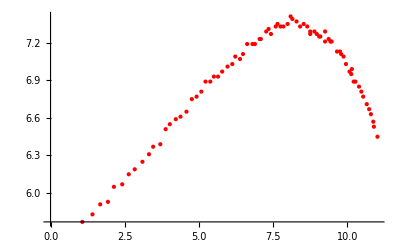

```mathematica
trial3experiment=ListPlot[trial3,PlotStyle->Red]
```

#### Modeling ω linearly

```mathematica
vx==D[-7.617+75.41*t-156.4*t^2+139.7t^3,t]/.t->.1624
```

vx==35.6645

```mathematica
vy==D[4.874+2.074*t+30.43*t^2-56.25*t^3,t]/.t->0.1624
```

vy==7.50709

```mathematica
ωinitial=308.4
```

308.4

```mathematica
ωfinal=146.5
```

146.5

```mathematica
slopeω=(146.5-308.4)/(.8442-.1624)
```

-237.46

```mathematica
ω0=195.738-slopeω*.2568
```

232.555

#### Modeling ω quadratically

```mathematica
Solve[146.5==a*.8442^2+b*.8442,a]
```

{{a→-1.40317 (-146.5+0.8442 b)}}

```mathematica
Solve[308.4==1.4031668127924588 (-146.5+0.8442 b)+b*.1624,b]
```

{{b→381.575}}

```mathematica
a=1.4031668127924588 (-146.5+0.8442 381.575)
```

246.432

```mathematica
b=381.575
```

381.575

#### Program

```mathematica
(*define constants and initial conditions*)
Manipulate[
g=9.8;
m=.01436;
r=.05;
c2=.0023048;
ρ=1.2041;
inertia=2/5*m*r^2;
vx=35.6645;
vy=7.50709;
x=1.072;
y=5.769;
ti=.1624;
tf=.8442;
dt=.01;
kenergy=0;
gpenergy=0;
renergy=0;
totalenergy=0;
energydiss=0;
systemenergy=0;

(* define an array where we store the results of the simulation *) 
modelpositiontrial3 ={{x,y}};
modelsystemenergytrial3={{ti,systemenergy}};
(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t≤tf,
(*ω=slopeω*(t-ti)+ωinitial;*)
ω=246.4320344442654*t^2+381.575*t;
θ=ArcTan[vy/vx];
v=Sqrt[vx^2+vy^2];

fd=c2*v^2;
fs=2*π*ρ*v*cl*r^3*ω ;
fg=-m*g;

ax=(fd*Cos[θ+π]+fs*Cos[θ+π/2])/m;
vx=vx+ax*dt;
x=x+vx*dt;

ay=(fd*Sin[θ+π]+fs*Sin[θ+π/2]+fg)/m;
vy=vy+ay*dt;
y=y+vy*dt;

kenergy=.5*m*v^2;
gpenergy=m*g*y;
renergy=.5*inertia*ω^2;
totalenergy=kenergy+gpenergy+renergy;
energydiss=-fd*v*dt;
systemenergy=totalenergy-energydiss;

t= t + dt;
(* add the results of the calculation step to the array *)
modelpositiontrial3 = Append[modelpositiontrial3,{x,y}];
modelsystemenergytrial3=Append[modelsystemenergytrial3,{t,systemenergy}];
];
(* plot the simulation and compare with the exact result *)
dataplottrial3 = ListPlot[modelpositiontrial3];

systemenergyplottrial3=ListPlot[modelsystemenergytrial3];
Show[{systemenergyplottrial3},PlotRange->All]
Show[{dataplottrial3,trial3experiment},PlotRange->All],{cl,0,.2}]
```

### Data

```mathematica
trial3data={{"VideoAnalysis: Time (s)","VideoAnalysis: X (m)","VideoAnalysis: Y (m)","VideoAnalysis: X Velocity (m/s)","VideoAnalysis: Y Velocity (m/s)"},{0.162363524955,1.07195825537,5.76869083576,39.2057650126,7.67983709104},{0.170512106358,1.41270788779,5.82882312384,35.851138744,7.97478028663},{0.178539067142,1.6732811361,5.90899950793,32.5240727907,7.21204314835},{0.186687648544,1.93385438441,5.92904360396,29.7879378041,8.07846850109},{0.194836229947,2.13429534466,6.0493081801,29.5106967845,8.00979834617},{0.202984811349,2.414912689,6.06935227613,29.6118283681,6.93717570785},{0.211011772133,2.63539774526,6.14952866022,27.6137689915,7.07649404881},{0.219160353535,2.8358387055,6.18961685227,27.935129579,6.6425448137},{0.227308934938,3.09641195382,6.24974914035,27.5897327877,7.05174815181},{0.23545751634,3.31689701008,6.30988142842,24.2467692362,7.00799514115},{0.243484477124,3.45720568225,6.37001371649,23.8378397657,6.38609427029},{0.251633058526,3.69773483454,6.39005781251,23.9609820752,7.94112819124},{0.259781639929,3.87813169876,6.51032238866,21.2974483734,8.21299121949},{0.267930221331,4.01844037093,6.55041058071,21.3644159863,5.70059209326},{0.275957182115,4.21888133117,6.59049877276,21.993328987,4.53507673674},{0.284105763518,4.37923409937,6.61054286878,22.2815579841,4.80284966538},{0.29225434492,4.57967505961,6.65063106083,22.6129093322,7.08155388937},{0.300281305704,4.76007192383,6.75085154095,21.1591758136,6.80249841817},{0.308429887106,4.92042469202,6.77089563697,19.8569182695,5.27529128124},{0.316578468509,5.08077746021,6.81098382902,18.7615277653,6.09139474918},{0.324727049911,5.22108613238,6.89116021312,18.274502038,4.74083773538},{0.332754010695,5.38143890058,6.89116021312,17.3806695119,3.15866940621},{0.340902592097,5.50170347672,6.93124840517,16.7770144132,2.73962786467},{0.3490511735,5.64201214889,6.93124840517,17.6663944527,2.94512394627},{0.357199754902,5.78232082106,6.97133659722,19.1685911143,4.19207682345},{0.365226715686,5.96271768528,7.01142478926,19.5136627284,3.98425957484},{0.373375297089,6.12307045347,7.03146888529,17.0511806498,4.10662420554},{0.381523878491,6.22329093359,7.09160117336,16.228167557,3.01405129279},{0.389672459893,6.38364370179,7.07155707734,16.0753304394,2.88209669971},{0.397699420677,6.48386418191,7.11164526939,16.0112749526,5.29560967673},{0.40584800208,6.62417285408,7.19182165348,17.8179516764,4.17967822015},{0.413996583482,6.8045697183,7.19182165348,16.2190915598,1.7838808786},{0.422023544266,6.88474610239,7.19182165348,14.8387468249,2.26715740577},{0.430172125668,7.04509887059,7.23190984553,13.3540169739,2.67070051815},{0.438320707071,7.08518706263,7.23190984553,13.6256228106,3.35407009279},{0.446469288473,7.26558392685,7.2920421336,14.3613184467,3.36932028089},{0.454496249257,7.34576031095,7.31208622963,12.1554418214,0.820179466709},{0.46264483066,7.42593669505,7.27199803758,13.554906639,1.57556720553},{0.470793412062,7.58628946324,7.33213032565,12.8710226811,2.80292002826},{0.478941993464,7.64642175131,7.35217442168,11.469426544,0.754257634903},{0.486968954248,7.74664223143,7.33213032565,12.5713328689,0.0656652815901},{0.495117535651,7.84686271155,7.33213032565,13.8288156839,1.43822689567},{0.503266117053,7.98717138372,7.35217442168,13.6919897572,3.14575641972},{0.511414698455,8.08739186384,7.41230670975,11.7436787248,1.65066723683},{0.519441659239,8.14752415192,7.39226261372,12.8514074569,-1.37624380871},{0.527590240642,8.28783282409,7.3722185177,14.8041402579,-2.53312033406},{0.535738822044,8.40809740023,7.33213032565,14.8449110852,-1.71753124931},{0.543765782828,8.52836197638,7.35217442168,14.2222566559,-1.37126090427},{0.551914364231,8.64862655252,7.33213032565,12.3224330165,-3.14601361131},{0.560062945633,8.74884703264,7.27199803758,8.70110631202,-2.05318350697},{0.568211527035,8.74884703264,7.2920421336,9.41008638681,-0.34017401266},{0.576238487819,8.88915570481,7.2920421336,11.4086588639,-1.09932924905},{0.584387069222,8.96933208891,7.27199803758,10.1342124079,-1.84743023378},{0.592535650624,9.04950847301,7.25195394156,9.11005245853,-1.43796970408},{0.600684232026,9.08959666505,7.25195394156,10.7203230608,-1.23890414023},{0.60871119281,9.24994943325,7.21186574951,9.82417000906,0.82791069427},{0.616859774213,9.24994943325,7.2920421336,8.62961856562,0.0661097550552},{0.625008355615,9.37021400939,7.23190984553,9.72065984486,-2.87184737478},{0.633156937017,9.43034629747,7.21186574951,8.92543988149,-2.53960216142},{0.641183897802,9.47043448951,7.21186574951,12.5787901712,-4.12511914122},{0.649332479204,9.65083135373,7.13168936541,14.0436285028,-3.97315143841},{0.657481060606,9.75105183385,7.13168936541,10.2375519086,-2.47213137875},{0.66550802139,9.7911400259,7.11164526939,8.85874839903,-3.08991394833},{0.673656602793,9.87131641,7.09160117336,9.85978897982,-4.72388402512},{0.681805184195,9.95149279409,7.03146888529,11.0207748559,-5.81645693787},{0.689953765597,10.0717573702,6.97133659722,9.89524599257,-4.26057573111},{0.697980726381,10.1318896583,6.95129250119,6.52309208561,-1.50568164374},{0.706129307784,10.1519337543,6.99138069324,6.02810258559,-3.28591432104},{0.714277889186,10.2120660424,6.89116021312,7.73793531792,-4.65291066191},{0.722426470588,10.2721983305,6.89116021312,10.2382536313,-3.70743031813},{0.730453431373,10.3924629066,6.85107202107,11.2003285148,-4.67182572729},{0.738602012775,10.4726392907,6.81098382902,9.99943249796,-5.06697760817},{0.746750594177,10.5327715788,6.77089563697,10.8178391742,-5.81927452933},{0.754899175579,10.6530361549,6.7107633489,11.1318296072,-5.90866589209},{0.762926136364,10.733212539,6.67067515685,9.27694131436,-5.49723628183},{0.771074717766,10.7933448271,6.63058696481,8.43110137829,-6.03224657103},{0.779223299168,10.8735212112,6.57045467673,7.48919095926,-6.52858036504},{0.787250259952,10.8935653072,6.53036648468,-29.2235540834,3.47156808012},{0.795398841355,11.0138298834,6.45019010059,-104.063975015,24.5015220269},{0.803547422757,11.0940062675,6.37001371649,-333.357230681,91.2700791017},{0.811696004159,0.00962116609162,9.55702498434,6.66008990093,-7.553922427},{0.819722964944,11.1741826516,6.26979323637,352.043171446,-109.028357778},{0.827871546346,11.2744031317,6.16957275625,123.309100642,-42.8962382667},{0.836020127748,11.3345354198,6.06935227613,66.1212710966,-22.7173110217},{0.84416870915,11.4147118039,6.08939637215,9.42933470663,-1.6398842968}}
```

{{VideoAnalysis: Time (s),VideoAnalysis: X (m),VideoAnalysis: Y (m),VideoAnalysis: X Velocity (m/s),VideoAnalysis: Y Velocity (m/s)},{0.162364,1.07196,5.76869,39.2058,7.67984},{0.170512,1.41271,5.82882,35.8511,7.97478},{0.178539,1.67328,5.909,32.5241,7.21204},{0.186688,1.93385,5.92904,29.7879,8.07847},{0.194836,2.1343,6.04931,29.5107,8.0098},{0.202985,2.41491,6.06935,29.6118,6.93718},{0.211012,2.6354,6.14953,27.6138,7.07649},{0.21916,2.83584,6.18962,27.9351,6.64254},{0.227309,3.09641,6.24975,27.5897,7.05175},{0.235458,3.3169,6.30988,24.2468,7.008},{0.243484,3.45721,6.37001,23.8378,6.38609},{0.251633,3.69773,6.39006,23.961,7.94113},{0.259782,3.87813,6.51032,21.2974,8.21299},{0.26793,4.01844,6.55041,21.3644,5.70059},{0.275957,4.21888,6.5905,21.9933,4.53508},{0.284106,4.37923,6.61054,22.2816,4.80285},{0.292254,4.57968,6.65063,22.6129,7.08155},{0.300281,4.76007,6.75085,21.1592,6.8025},{0.30843,4.92042,6.7709,19.8569,5.27529},{0.316578,5.08078,6.81098,18.7615,6.09139},{0.324727,5.22109,6.89116,18.2745,4.74084},{0.332754,5.38144,6.89116,17.3807,3.15867},{0.340903,5.5017,6.93125,16.777,2.73963},{0.349051,5.64201,6.93125,17.6664,2.94512},{0.3572,5.78232,6.97134,19.1686,4.19208},{0.365227,5.96272,7.01142,19.5137,3.98426},{0.373375,6.12307,7.03147,17.0512,4.10662},{0.381524,6.22329,7.0916,16.2282,3.01405},{0.389672,6.38364,7.07156,16.0753,2.8821},{0.397699,6.48386,7.11165,16.0113,5.29561},{0.405848,6.62417,7.19182,17.818,4.17968},{0.413997,6.80457,7.19182,16.2191,1.78388},{0.422024,6.88475,7.19182,14.8387,2.26716},{0.430172,7.0451,7.23191,13.354,2.6707},{0.438321,7.08519,7.23191,13.6256,3.35407},{0.446469,7.26558,7.29204,14.3613,3.36932},{0.454496,7.34576,7.31209,12.1554,0.820179},{0.462645,7.42594,7.272,13.5549,1.57557},{0.470793,7.58629,7.33213,12.871,2.80292},{0.478942,7.64642,7.35217,11.4694,0.754258},{0.486969,7.74664,7.33213,12.5713,0.0656653},{0.495118,7.84686,7.33213,13.8288,1.43823},{0.503266,7.98717,7.35217,13.692,3.14576},{0.511415,8.08739,7.41231,11.7437,1.65067},{0.519442,8.14752,7.39226,12.8514,-1.37624},{0.52759,8.28783,7.37222,14.8041,-2.53312},{0.535739,8.4081,7.33213,14.8449,-1.71753},{0.543766,8.52836,7.35217,14.2223,-1.37126},{0.551914,8.64863,7.33213,12.3224,-3.14601},{0.560063,8.74885,7.272,8.70111,-2.05318},{0.568212,8.74885,7.29204,9.41009,-0.340174},{0.576238,8.88916,7.29204,11.4087,-1.09933},{0.584387,8.96933,7.272,10.1342,-1.84743},{0.592536,9.04951,7.25195,9.11005,-1.43797},{0.600684,9.0896,7.25195,10.7203,-1.2389},{0.608711,9.24995,7.21187,9.82417,0.827911},{0.61686,9.24995,7.29204,8.62962,0.0661098},{0.625008,9.37021,7.23191,9.72066,-2.87185},{0.633157,9.43035,7.21187,8.92544,-2.5396},{0.641184,9.47043,7.21187,12.5788,-4.12512},{0.649332,9.65083,7.13169,14.0436,-3.97315},{0.657481,9.75105,7.13169,10.2376,-2.47213},{0.665508,9.79114,7.11165,8.85875,-3.08991},{0.673657,9.87132,7.0916,9.85979,-4.72388},{0.681805,9.95149,7.03147,11.0208,-5.81646},{0.689954,10.0718,6.97134,9.89525,-4.26058},{0.697981,10.1319,6.95129,6.52309,-1.50568},{0.706129,10.1519,6.99138,6.0281,-3.28591},{0.714278,10.2121,6.89116,7.73794,-4.65291},{0.722426,10.2722,6.89116,10.2383,-3.70743},{0.730453,10.3925,6.85107,11.2003,-4.67183},{0.738602,10.4726,6.81098,9.99943,-5.06698},{0.746751,10.5328,6.7709,10.8178,-5.81927},{0.754899,10.653,6.71076,11.1318,-5.90867},{0.762926,10.7332,6.67068,9.27694,-5.49724},{0.771075,10.7933,6.63059,8.4311,-6.03225},{0.779223,10.8735,6.57045,7.48919,-6.52858},{0.78725,10.8936,6.53037,-29.2236,3.47157},{0.795399,11.0138,6.45019,-104.064,24.5015},{0.803547,11.094,6.37001,-333.357,91.2701},{0.811696,0.00962117,9.55702,6.66009,-7.55392},{0.819723,11.1742,6.26979,352.043,-109.028},{0.827872,11.2744,6.16957,123.309,-42.8962},{0.83602,11.3345,6.06935,66.1213,-22.7173},{0.844169,11.4147,6.0894,9.42933,-1.63988}}

```mathematica
trial3=Table[{trial3data[[n,2]],trial3data[[n,3]]},{n,2,80}]
```

{{1.07196,5.76869},{1.41271,5.82882},{1.67328,5.909},{1.93385,5.92904},{2.1343,6.04931},{2.41491,6.06935},{2.6354,6.14953},{2.83584,6.18962},{3.09641,6.24975},{3.3169,6.30988},{3.45721,6.37001},{3.69773,6.39006},{3.87813,6.51032},{4.01844,6.55041},{4.21888,6.5905},{4.37923,6.61054},{4.57968,6.65063},{4.76007,6.75085},{4.92042,6.7709},{5.08078,6.81098},{5.22109,6.89116},{5.38144,6.89116},{5.5017,6.93125},{5.64201,6.93125},{5.78232,6.97134},{5.96272,7.01142},{6.12307,7.03147},{6.22329,7.0916},{6.38364,7.07156},{6.48386,7.11165},{6.62417,7.19182},{6.80457,7.19182},{6.88475,7.19182},{7.0451,7.23191},{7.08519,7.23191},{7.26558,7.29204},{7.34576,7.31209},{7.42594,7.272},{7.58629,7.33213},{7.64642,7.35217},{7.74664,7.33213},{7.84686,7.33213},{7.98717,7.35217},{8.08739,7.41231},{8.14752,7.39226},{8.28783,7.37222},{8.4081,7.33213},{8.52836,7.35217},{8.64863,7.33213},{8.74885,7.272},{8.74885,7.29204},{8.88916,7.29204},{8.96933,7.272},{9.04951,7.25195},{9.0896,7.25195},{9.24995,7.21187},{9.24995,7.29204},{9.37021,7.23191},{9.43035,7.21187},{9.47043,7.21187},{9.65083,7.13169},{9.75105,7.13169},{9.79114,7.11165},{9.87132,7.0916},{9.95149,7.03147},{10.0718,6.97134},{10.1319,6.95129},{10.1519,6.99138},{10.2121,6.89116},{10.2722,6.89116},{10.3925,6.85107},{10.4726,6.81098},{10.5328,6.7709},{10.653,6.71076},{10.7332,6.67068},{10.7933,6.63059},{10.8735,6.57045},{10.8936,6.53037},{11.0138,6.45019}}